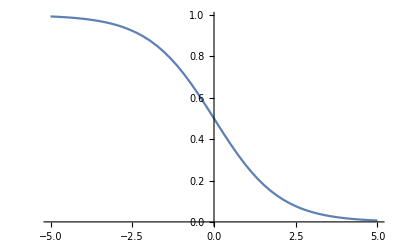

```mathematica
F[x_]:=1/(1+Exp[x]);
Plot[F[x],{x,-5,5}]
```

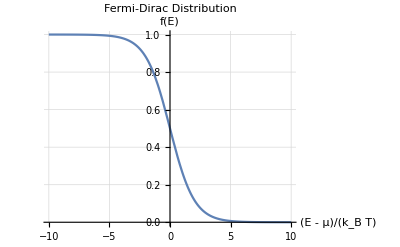

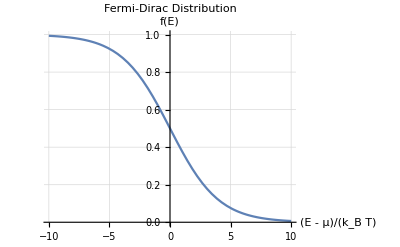

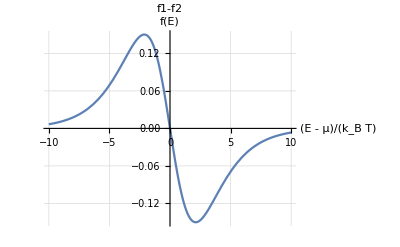

```mathematica
Plot[1/(1+Exp[x]),{x,-10,10},AxesLabel->{"(E - μ)/(k_B T)","f(E)"},PlotLabel->"Fermi-Dirac Distribution",GridLines->Automatic]
Plot[1/(1+Exp[x/2]),{x,-10,10},PlotRange->{0,1},AxesLabel->{"(E - μ)/(k_B T)","f(E)"},PlotLabel->"Fermi-Dirac Distribution",GridLines->Automatic]
Plot[(1/(1+Exp[x]))-(1/(1+Exp[x/2])),{x,-10,10},AxesLabel->{"(E - μ)/(k_B T)","f(E)"},PlotLabel->"f1-f2",GridLines->Automatic]
```

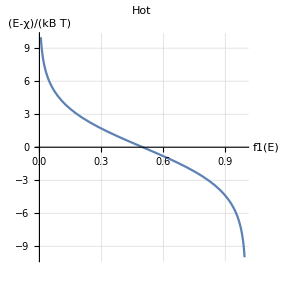

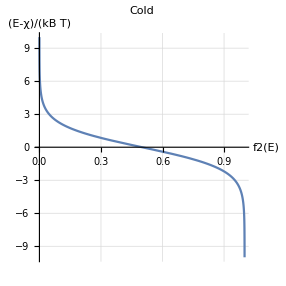

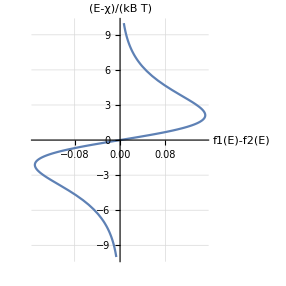

```mathematica
ParametricPlot[{1/(1+Exp[x/2]),x},{x,-10,10},AspectRatio->1,AxesLabel->{"f1(E)","(E-χ)/(kB T)"},PlotLabel->"Hot",GridLines->Automatic]
ParametricPlot[{1/(1+Exp[x]),x},{x,-10,10},AspectRatio->1,AxesLabel->{"f2(E)","(E-χ)/(kB T)"},PlotLabel->"Cold",GridLines->Automatic]
ParametricPlot[{(1/(1+Exp[x/2]))-(1/(1+Exp[x])),x},{x,-10,10},AspectRatio->1,AxesLabel->{"f1(E)-f2(E)","(E-χ)/(kB T)"},GridLines->Automatic]
```